## MAP-Kinase Oscillations in Solution Under continuous stimuli - Mass Action Kinetics

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 13:47:48.408735 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

xCellerator Implementation
Created: 12-Aug-2005 BES
Revised: 15 Oct 2007 BES - verify under Mathematica 6.0

This notebook has two models:
Model (1) is purely mass action. It assumes that Kpp inhibits the activity of the KKK-S complex (S is the input signal)

Model (2) is mass action except for one rate constant ((KKK⇄KKKp)^S) which use the standard competitive inhibition hill function: it assumes that S has two binding sites, one for KKK and the other for Kpp, but is only active if Kpp is not bound.

It is broadly based on Kholodenko's model but uses only Mass Action Kinetics and does not use any Michaelis Approximations

## Model 1

## Rate Constants & Initial Conditions

```mathematica
model1RateConstants={a0-> 1,d0-> 1,a1->1 , d1->7.5,  k1->2.5  , a3-> 1, d3-> 10 , k3->0.025 , 
a4-> 1, d4->1, k4->1, a5-> 1, d5-> 1, k5-> 1,a6-> 1, d6->  1, k6-> 1, a7-> 1, d7-> 1};
model1InitialConditions={KKK-> 100,KKKp-> 0, KK-> 300, KKp-> 0, KKpp-> 0, MAPK-> 300, Kp-> 0, Kpp-> 0,S-> 1, Kph-> 1, KKph-> 1, KKKph-> 10};
```

```mathematica
(* need to make sure compounds are defined consistently *) 

model1={

(* Maintain a sustained signal (S) *) 

{∅⇄S, a0,d0},

(* phosphorylation reactions *) 

{Overscript[KKK⇄KKKp, S],{a1,d1,k1}},


{Overscript[KK⇄KKp, KKKp],{a3,d3,k3}},{Overscript[KKp⇄KKpp, KKKp],{a3,d3,k3}},
{Overscript[MAPK⇄Kp, KKpp],{a3,d3,k3}},{Overscript[Kp⇄Kpp, KKpp],{a3,d3,k3}},

(* add in some competitive inhibition for Bind[KKK,S] produced by Kpp *) 

 {Bind[KKK,S]+Kpp⇄KKK$S$Kpp, a7, d7},  

(* dephosphorylation reactions *) 

{Overscript[KKKp⇄KKK, KKKph], {a4,d4,k4}},
{Overscript[KKp⇄KK, KKph], {a5,d5,k5}},{Overscript[KKpp⇄KKp, KKph], {a5,d5,k5}},
{Overscript[Kpp⇄Kp, Kph],{a6,d6,k6}},{Overscript[Kp⇄MAPK, Kph], {a6,d6,k6}}

};
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {KKK$S$Kpp,Bind[KK,KKKp],Bind[KKK,S],Bind[KKKp,KKKph],Bind[KKKp,KKp],Bind[KKp,KKph],Bind[KKph,KKpp],Bind[KKpp,Kp],Bind[KKpp,MAPK],Bind[Kp,Kph],Bind[Kph,Kpp]}

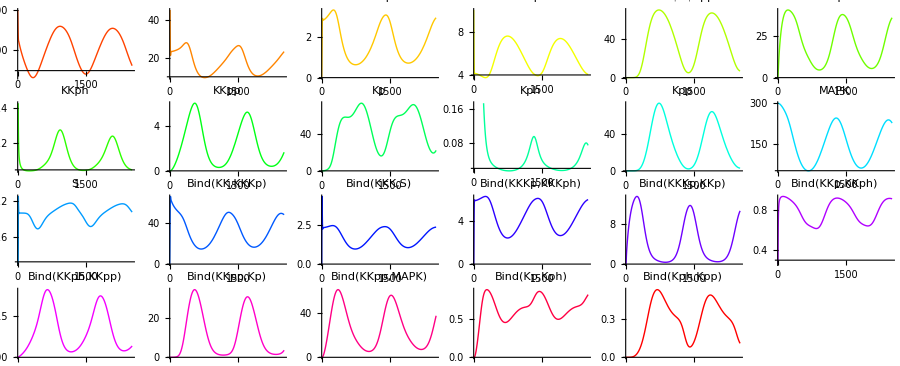

```mathematica
sim=run[model1,
initialConditions->model1InitialConditions,
rates-> model1RateConstants,
timeSpan->2500,MaxSteps->25000,gridPlotVariables-> All, plotColumns-> 6, ImageSize-> 900, plot-> True, plotVariables-> None];
```

## Model 2

```mathematica
model2RateConstants={a1->1,d1->7.5,k1->2.5*10/(10+Kpp[t]),a3->1,d3->14.975,k3->0.025,a4->1,d4->1,k4->1,a5->1,d5->1,k5->1,a6->1,d6->1,k6->1};
```

```mathematica
model2={

(* phosphorylation reactions *) 
(* Non-competitive inhibition of first stage of cascade by Kpp (MAPK-pp)  *)

{∅⇄S, 1,1},

{Overscript[KKK⇄KKKp, S],{a1,d1,k1}},


{Overscript[KK⇄KKp, KKKp],{a3,d3,k3}},{Overscript[KKp⇄KKpp, KKKp],{a3,d3,k3}},
{Overscript[MAPK⇄Kp, KKpp],{a3,d3,k3}},{Overscript[Kp⇄Kpp, KKpp],{a3,d3,k3}},

(* dephosphorylation reactions *) 

{Overscript[KKKp⇄KKK, KKKph], {a4,d4,k4}},
{Overscript[KKp⇄KK, KKph], {a5,d5,k5}},{Overscript[KKpp⇄KKp, KKph], {a5,d5,k5}},
{Overscript[Kpp⇄Kp, Kph],{a6,d6,k6}},{Overscript[Kp⇄MAPK, Kph], {a6,d6,k6}}

};
```

```mathematica
model2InitialConditions={KKK-> 100,KKKp-> 0, KK-> 300, KKp-> 0, KKpp-> 0, MAPK-> 300, Kp-> 0, Kpp-> 0,S-> 1, Kph-> 1, KKph-> 1, KKKph-> 10}
```

{KKK→100,KKKp→0,KK→300,KKp→0,KKpp→0,MAPK→300,Kp→0,Kpp→0,S→1,Kph→1,KKph→1,KKKph→10}

## Predict a Time Course

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Bind[KK,KKKp],Bind[KKK,S],Bind[KKKp,KKKph],Bind[KKKp,KKp],Bind[KKp,KKph],Bind[KKph,KKpp],Bind[KKpp,Kp],Bind[KKpp,MAPK],Bind[Kp,Kph],Bind[Kph,Kpp]}

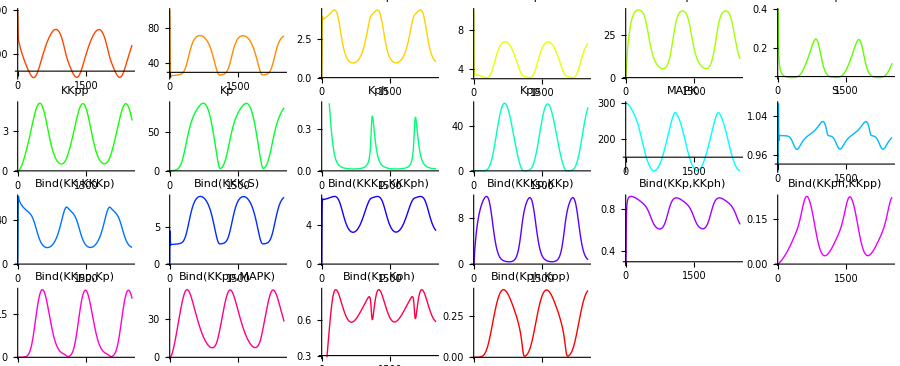

```mathematica
sim=run[model2,
initialConditions->model2InitialConditions, rates-> model2RateConstants,
timeSpan->2500,MaxSteps->25000,gridPlotVariables-> All, plotColumns-> 6, ImageSize-> 900, plot-> True, plotVariables-> None];
```